## Integration limits

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

```mathematica
Get["results/FisherMatrix-1_Output_k1k2k3_NInt"];
```

```mathematica
Pvals
```

{1,2,5}

```mathematica
Νvals
```

{2,4,8,16,32,64,128}

In the following we semi-arbitrarily assume that the experiment is designed with prey replacement (i.e. Poisson process) and in such a way that the maximum expected number of eaten prey in the highest prey treatment equals the number of prey in that treatment, i.e. λ (of Poisson) ≤ E[F(N_max,P)PT] = N_max.  This allows us to set a maximum value for ‘a’ and ‘h’.
Similarly, we semi-arbitrarily assume that the minimum expected number of eaten prey in the N_max treatment is a single prey, i.e. λ (of Poisson) ≥ E[F(N_max,P)PT] = 1.  This allows us to set a maximum value for γ and ‘m’ .

#### Holling Type I

```mathematica
limH1=Solve[H1==Nmax,a]
```

{{a→Nmax/(P T Ν)}}

Since the rhs is a decreasing function of both N and P, the maximum permissible ‘a’ occurs when N = N_max and P = P_max.

```mathematica
limH1a[Pmax_, T_] = limH1[[1, 1, 2]] /. {Ν -> Nmax, P -> Pmax}
```

1/(Pmax T)

#### Ratio

```mathematica
limR=Solve[R==Nmax,a]
```

{{a→Nmax/(T Ν)}}

```mathematica
limRa[T_]=limR[[1,1,2]]/.{Ν-> Nmax, P-> Pmax}
```

1/T

#### Holling Type II

```mathematica
limH2=Solve[H2==Nmax,a]
```

{{a→-Nmax/((h Nmax-P T) Ν)}}

Since N and P are only in the denominator, the rhs  is smallest at N = N_max and P = P_max.

```mathematica
limH2a[h_,Nmax_,Pmax_,T_]=limH2[[1,1,2]]/.{Ν-> Nmax, P-> Pmax}
```

-1/(h Nmax-Pmax T)

Moreover, the rhs must stay positive which means there is an additional  limit imposed by the denominator of h N_max < P_max T.  Therefore, h can not exceed:

```mathematica
limH2h[Nmax_,Pmax_,T_]=Solve[Denominator[limH2a[h,Nmax,Pmax,T]]==0,h][[1,1,2]]
```

(Pmax T)/Nmax

```mathematica
Manipulate[
RegionPlot[
 a<limH2a[h,Nmax,Pmax,T] && h< limH2h[Nmax,Pmax,T],
{a,0,5},{h,0,1},
FrameLabel->Automatic],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

#### Arditi-Ginzburg

```mathematica
limAG=Solve[AG==Nmax,a]
```

{{a→-(Nmax P)/((h Nmax-P T) Ν)}}

```mathematica
limAGa[h_,Nmax_,Pmax_,T_]=limAG[[1,1,2]]/.{Ν-> Nmax, P-> Pmax}
```

-Pmax/(h Nmax-Pmax T)

```mathematica
limAGh[Nmax_,Pmax_,T_]=Solve[Denominator[limAGa[h,Nmax,Pmax,T]]==0,h][[1,1,2]]
```

(Pmax T)/Nmax

```mathematica
Manipulate[
RegionPlot[
 a<limAGa[h,Nmax,Pmax,T] && h< limAGh[Nmax,Pmax,T] ,
{a,0,5},{h,0,1},
FrameLabel->Automatic],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

#### Hassell-Varley

```mathematica
limHV=Solve[HV==Nmax,a]//Simplify
```

{{a→(Nmax P^(-1+m))/(T Ν)}}

This is always most restrictive for N = Nmax.

```mathematica
limHVa[m_,P_,T_]=(Solve[HV==Nmax,a]/.Ν-> Nmax)[[1,1,2]];
```

```mathematica
Manipulate[
Plot[limHVa[m,P,T],{P,1,10},AxesLabel->Automatic],
{{T,1,"T"},1,10,1},
{{m,0.9,"m"},0,2,0.1}]
```

If m>1 then the limit is most restrictive at P = Pmin = 1.
If m=1 then the limit is universal (at a=1/T). [ Which can be subsumed into the the first since Pmin=1.] 
If m < 1 then the limit is most restrictive for P = P_max.

```mathematica
limHVa2[m_,Pmax_,T_]=
Boole[m≥1 ]*(limHVa[m,1,T]) + 
Boole[m<1 ]*(limHVa[m,Pmax,T])
```

Boole[m≥1]/T+(Pmax^(-1+m) Boole[m<1])/T

Now how to limit m?
There is no natural boundary, so we inform ourselves empirically, observing that estimates rarely exceed a value of 4 or 5.  (We will subsequently use the boundary on m to set the corresponding boundary for γ.)

```mathematica
limHVm2=5;
```

```mathematica
Manipulate[
RegionPlot[
 a<limHVa2[m,Pmax,T]&& m< limHVm2 ,
{a,0,5},{m,0,5},
FrameLabel->Automatic],
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

#### Arditi-Akcakaya

```mathematica
limAA=Solve[AA==Nmax,a]
```

{{a→-(Nmax P^m)/((h Nmax-P T) Ν)}}

```mathematica
limAAa[h_,m_,Nmax_,P_,T_]=limAA[[1,1,2]]/.Ν-> Nmax
```

-P^m/(h Nmax-P T)

```mathematica
limAAh=Solve[Denominator[limAAa[h,m,Nmax,P,T]]==0,h]
```

{{h→(P T)/Nmax}}

```mathematica
limAAh2[Nmax_,Pmax_,T_]=(Solve[Denominator[limAAa[h,m,Nmax,Pmax,T]]==0,h])[[1,1,2]]
```

(Pmax T)/Nmax

```mathematica
Manipulate[
Plot[limAAa[h,m,Nmax,P,T],{P,1,10},AxesLabel->Automatic],
{{T,1,"T"},1,10,1},
{{Nmax,1,"Nmax"},1,10,1},
{{m,1.5,"m"},0,2,0.1},
{{h,0.9,"h"},0,1,0.1}]
```

```mathematica
Minimize[{limAAa[h,m,Nmax,P,T],T>0&& 0≤ h < limAAh2[Nmax,P,T] && Nmax>0  && 1≤ P ≤ Pmax && Pmax > 1 },P]
```

Minimize[{-P^m/(h Nmax-P T),T>0&&0≤h<(P T)/Nmax&&Nmax>0&&1≤P≤Pmax&&Pmax>1},P]

Since Minimize can' t do it, solve for the minimum ‘a’ by solving for it by taking the derivative with respect to P and then substituting this value of P back in to calculate min ‘a’.  (I think this will only be correct if m > 1.)

```mathematica
Psol=Solve[D[limAAa[h,m,Nmax,P,T],P]==0,P][[1,1,2]]
```

(h m Nmax)/((-1+m) T)

Note that even when m > 1, the minimum may exist at a P > Pmax.  In this case the maximum restriction on ‘a’ is at Pmax.

```mathematica
limAAa2[h_,m_,Nmax_,Pmax_,T_]=
If[h==0|| Pmax== 1, limAAa[h,m,Nmax,Pmax,T],0]+
If[m≤ 1 &&h>0 &&Pmax>1,  limAAa[h,m,Nmax,Pmax,T], 0]+If[m>1&&h>0 &&Pmax>1&&Pmax ≤ (h m Nmax)/((m-1) T) , limAAa[h,m,Nmax,Pmax,T],0]+If[m>1&&h>0 &&Pmax>1&&Pmax > (h m Nmax)/((m-1) T), limAAa[h,m,Nmax,(h m Nmax)/((m-1) T),T],0];
```

```mathematica
Manipulate[
{limAAa2[h,m,Nmax,Pmax,T],
limAAa[h,m,Nmax,Pmax,T],
If[m≠1,(h m Nmax)/((m-1) T),NA],

If[h==0|| Pmax== 1, limAAa[h,m,Nmax,Pmax,T],0],
If[m≤ 1 &&h>0 &&Pmax>1,  limAAa[h,m,Nmax,Pmax,T], 0],If[m>1&&h>0 &&Pmax>1&&Pmax ≤ (h m Nmax)/((m-1) T) , limAAa[h,m,Nmax,Pmax,T],0],If[m>1&&h>0 &&Pmax>1&&Pmax > (h m Nmax)/((m-1) T), limAAa[h,m,Nmax,(h m Nmax)/((m-1) T),T],0]
},
{{m,1.1,"m"},0,2,0.05},
{{h,0.1,"h"},0,1},
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,4,"Pmax"},1,20,1},
{{T,1,"T"},1,10,1}]
```

Apply the same limit to AA as applied to HV.

```mathematica
limAAm2=limHVm2;
```

```mathematica
Manipulate[
RegionPlot3D[
a<limAAa2[h,m,Nmax,Pmax,T] && h< limAAh2[Nmax,Pmax,T] && m < limAAm2,
{a,0,5},{m,0,5},{h,0,0.1}, 
AxesLabel->Automatic],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

#### Beddington-DeAngelis

```mathematica
BD
```

(a P T Ν)/(1+(-1+P) γ+a h Ν)

```mathematica
limBD=Solve[BD==Nmax,a]//Simplify
```

{{a→(Nmax (-1+γ-P γ))/((h Nmax-P T) Ν)}}

Again, since N is only in the denominator, the most restrictive value is always N = N_max.

```mathematica
limBDa[h_,γ_,Nmax_,P_,T_]=limBD[[1,1,2]]/.Ν-> Nmax
```

(-1+γ-P γ)/(h Nmax-P T)

The part that depends on P is not monotonically increasing or decreasing but rather depends on the values of γ and h;  P = P_max need not be the most restrictive case.   We can use Minimize[] to find the most restrictive case, noting that there is still the limit imposed by the denominator that h N_max < P T.

For ‘a’ to stay positive when P ≥ 1 , h cannot exceed:

```mathematica
limBDh=Solve[Denominator[limBDa[h,γ,Nmax,P,T]]==0 ,h]
```

{{h→(P T)/Nmax}}

This is equivalent to saying that the total time handling prey for all predators can' t exceed the total time of the experiment. Now convert this to a function:

```mathematica
limBDh2[Nmax_,P_,T_]=(Solve[Denominator[limBD[[1,1,2]]]==0,h])[[1,1,2]];
```

We limit γ by applying the equivalent limit as we applied to m (for the HV and AA models).

```mathematica
Solve[Denominator[BD]-Denominator[AA]==0,γ]//Simplify
```

{{γ→(-1+P^m)/(-1+P)}}

```mathematica
limBDγ2[P_]=limBDγ[[1,1,2]];
```

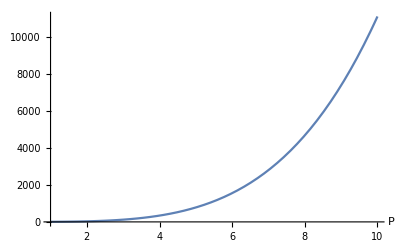

```mathematica
Plot[limBDγ2[P],{P,1,10},AxesLabel->Automatic]
```

```mathematica
minlimBDa=Minimize[{limBDa[h,γ,Nmax,P,T],T>0&& 0 ≤ γ <limBDγ2[Pmax] && 0≤ h < limBDh2[Nmax,P,T] && Nmax>0  && 1≤ P ≤ Pmax && Pmax > 1},P]
```

{Piecewise[{{1/(-h Nmax+T), Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&0≤h<(-T+T γ)/(Nmax γ)}, {(-1+γ-Pmax γ)/(h Nmax-Pmax T), (Pmax>1&&0≤γ<1&&T>0&&Nmax>0&&0≤h<(Pmax T)/Nmax)||(Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&h==(-T+T γ)/(Nmax γ))||(Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&(-T+T γ)/(Nmax γ)<h<(Pmax T)/Nmax)}, {∞, True}}],{P→Piecewise[{{1, Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&0≤h<(-T+T γ)/(Nmax γ)}, {Pmax, (Pmax>1&&0≤γ<1&&T>0&&Nmax>0&&0≤h<(Pmax T)/Nmax)||(Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&(-T+T γ)/(Nmax γ)<h<(Pmax T)/Nmax)}, {(1+Pmax)/2, Pmax>1&&1≤γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&h==(-T+T γ)/(Nmax γ)}, {Indeterminate, True}}]}}

Convert the above into a function :

```mathematica
limBDa2[h_,γ_,Nmax_,Pmax_,T_]=
First@minlimBDa/.{Ν-> Nmax,P-> Pmax};
```

```mathematica
Manipulate[
RegionPlot3D[
a<limBDa2[h,γ,Nmax,Pmax,T] && h< limBDh2[Nmax,Pmax,T] && γ < limBDγ2[Pmax],
{a,0,5},{γ,0,1},{h,0,1}, 
AxesLabel->Automatic],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

#### Crowley-Martin - limits on γ and h need to be checked!

```mathematica
limCM=Solve[CM==Nmax,a]//FullSimplify
```

{{a→(Nmax (-1+γ-P γ))/((-P T+h Nmax (1+(-1+P) γ)) Ν)}}

Again, since N is only in the denominator, the most restrictive value is always N = N_max.

```mathematica
limCMa[h_,γ_,Nmax_,P_,T_]=limCM[[1,1,2]]/.Ν-> Nmax//FullSimplify
```

(-1+γ-P γ)/(-P T+h Nmax (1+(-1+P) γ))

The limit for h is more complicated:

```mathematica
limCMh=Solve[Denominator[limCMa[h,γ,Nmax,P,T]]==0 ,h]
```

{{h→(P T)/(Nmax (1-γ+P γ))}}

```mathematica
limCMh2[γ_,Nmax_,P_,T_]=(Solve[Denominator[limCM[[1,1,2]]]==0,h])[[1,1,2]];
```

We limit γ by applying the equivalent limit as we applied to BD and m (for the HV and AA models).

```mathematica
limCMγ=limBDγ
```

{{γ→P^5/(-1+P)}}

```mathematica
Solve[Denominator[CM]-Denominator[AA]==0,γ]//Simplify
```

{{γ→(-1+P^m)/((-1+P) (1+a h Ν))}}

```mathematica
limCMγ2[P_]=limCMγ[[1,1,2]];
```

```mathematica
minlimCMa=Minimize[{limCMa[h,γ,Nmax,P,T],T>0&& 0 ≤ γ < limCMγ2[Pmax] && 0≤ h <limCMh2[γ,Nmax,Pmax,T] && Nmax>0  && 1≤ P ≤ Pmax && Pmax > 1},P]
```

{Piecewise[{{1/(-h Nmax+T), (Pmax>1&&γ==1&&T>0&&Nmax>0&&0≤h<T/Nmax)||(Pmax>1&&1<γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&0≤h<(Pmax T)/(Nmax-Nmax γ+Nmax Pmax γ))}, {(-1+γ-Pmax γ)/(h Nmax-Pmax T-h Nmax γ+h Nmax Pmax γ), Pmax>1&&0≤γ<1&&T>0&&Nmax>0&&0≤h≤T/Nmax}, {-∞, Pmax>1&&0≤γ<1&&T>0&&Nmax>0&&T/Nmax<h<(Pmax T)/(Nmax-Nmax γ+Nmax Pmax γ)}, {∞, True}}],{P→Piecewise[{{1, Pmax>1&&1<γ<Pmax^5/(-1+Pmax)&&T>0&&Nmax>0&&0≤h<(Pmax T)/(Nmax-Nmax γ+Nmax Pmax γ)}, {Pmax, Pmax>1&&0≤γ<1&&T>0&&Nmax>0&&0≤h≤T/Nmax}, {(1+Pmax)/2, Pmax>1&&γ==1&&T>0&&Nmax>0&&0≤h<T/Nmax}, {Indeterminate, True}}]}}

```mathematica
limCMa2[h_,γ_,Nmax_,Pmax_,T_]= First@minlimBDa;
```

```mathematica
Manipulate[
RegionPlot3D[
a<limCMa2[h,γ,Nmax,Pmax,T] && h< limCMh2[γ,Nmax,Pmax,T] && γ < limCMγ2[Pmax],
{a,0,5},{γ,0,1},{h,0,1}, 
AxesLabel->Automatic],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```

## Combined plots

We can compare the possible parameter volume of models with different parameter interpretations, hence split by Holling and Ratio type

#### Holling-type models

```mathematica
Manipulate[
pBD=RegionPlot3D[
a<limBDa2[h,γ,Nmax,Pmax,T] && h< limBDh2[Nmax,Pmax,T] && γ < limBDγ2[Pmax],
{a,0,10},{γ,0,10},{h,0,1}, 
AxesLabel->Automatic,
PlotStyle->None,
PlotLegends-> {"BD",""}, Mesh-> 10];
pCM=RegionPlot3D[
a<limCMa2[h,γ,Nmax,Pmax,T] && h< limCMh2[γ,Nmax,Pmax,T] && γ < limCMγ2[Pmax],
{a,0,5},{γ,0,1},{h,0,1}, 
AxesLabel->Automatic,
PlotStyle->{Glow@Blue,Opacity[0.1]},
PlotLegends-> {"CM",""},Mesh-> 0];
pH2=RegionPlot3D[
 a<limH2a[h,Nmax,Pmax,T] && h< limH2h[Nmax,Pmax,T] &&  γ < 0.1,
{a,0,5},{γ,0,1},{h,0,1},
AxesLabel->Automatic,
PlotStyle->{Red},
PlotLegends-> {"H2",""},Mesh-> 0];
Show[pBD,pCM,pH2],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,3,"T"},1,10,1}]
```

#### Ratio-type models

```mathematica
Manipulate[
pAA=RegionPlot3D[
a<limAAa2[h,m,Nmax,Pmax,T] && h< limAAh2[Nmax,Pmax,T] && m < limAAm2,
{a,0,5},{m,0,5},{h,0,1}, 
AxesLabel->Automatic,
PlotStyle->None,
PlotLegends-> {"BD",""}, Mesh-> 10];
pAG=RegionPlot3D[
a<limAGa[h,Nmax,Pmax,T] && h< limAGh[Nmax,Pmax,T] && m < 0.1,
{a,0,5},{m,0,5},{h,0,1}, 
AxesLabel->Automatic,
PlotStyle->{Glow@Blue,Opacity[0.1]},
PlotLegends-> {"AG",""},Mesh-> 0];
pHV=RegionPlot3D[
 a<limHVa2[m,Pmax,T]&& m< limHVm2 &&h<0.1,
{a,0,5},{m,0,5},{h,0,1}, 
AxesLabel->Automatic,
PlotStyle->{Red},
PlotLegends-> {"HV",""},Mesh-> 0];
Show[pAA,pAG,pHV],
{{Nmax,10,"Nmax"},1,20,1},
{{Pmax,2,"Pmax"},1,4,1},
{{T,1,"T"},1,10,1}]
```